Name : Vimal Joshi
Roll No. : 20201430
Course: Bsc. (h) Computer Science
Lagrange interpolation polynomial
P1

```mathematica
LagrangePolynomial[x0_,f0_]:=
Module[{xi=x0,fi=f0,n,m,polynomial},
n=Length[xi];
m=length[fi];
if[n≠m,
Print["List of points and function values are not of samesize"];
Return[];];
For[i=1,i≤n,i++,
L[i,x_]=(∏_(j=1)^(i-1) (x-xi[[j]])/(xi[[i]]-xi[[j]]))(∏_(j=i+1)^n (x-xi[[j]])/(xi[[i]]-xi[[j]]));];
polynomial[x_]=∑_(k=1)^n L[k,x]*fi[[k]];
Return[polynomial[x]];]


nodes={0,1,3};
values={1,3,55};
LagrangePolynomial[x_]=LagrangePolynomial[nodes,values]
```

List of points and function values are not of samesize

1/3 (1-x) (3-x)+3/2 (3-x) x+55/6 (-1+x) x

```mathematica
Expand[1/3(1-x)(3-x)+3/2(3-x)x+55/6(-1+x)x]
```

1-6 x+8 x^2

```mathematica
Q-2
```

```mathematica
nodes={0,1,3}
values={1,3};
lagrangePolynomial[x_]=LagrangePolynomial[nodes,values]
```

{0,1,3}

List of points and function values are not of samesize

Part::partw: Part 3 of {1,3} does not exist.

1/3 (1-x) (3-x)+3/2 (3-x) x+1/6 (-1+x) x {1,3}⟦3⟧

```mathematica
P-2
```

```mathematica
nodes={1,3,5,7,9};
values={N[Log[1]],N[Log[3]],N[Log[5]],N[Log[7]],N[Log[9]]};
lagrangePolynomial[x_]=LagrangePolynomial[nodes,values]
```

List of points and function values are not of samesize

0.+0.0114439 (5-x) (7-x) (9-x) (-1+x)+0.0251475 (7-x) (9-x) (-3+x) (-1+x)+0.0202699 (9-x) (-5+x) (-3+x) (-1+x)+0.00572194 (-7+x) (-5+x) (-3+x) (-1+x)

```mathematica
Simplify[0.+0.011443878006959476 (5-x) (7-x) (9-x) (-1+x)+0.025147467381782817 (7-x) (9-x) (-3+x) (-1+x)+0.020269897385992844 (9-x) (-5+x) (-3+x) (-1+x)+0.005721939003479738 (-7+x) (-5+x) (-3+x) (-1+x)]
```

-0.987583+1.18991 x-0.223608 x^2+0.0221231 x^3-0.000844369 x^4

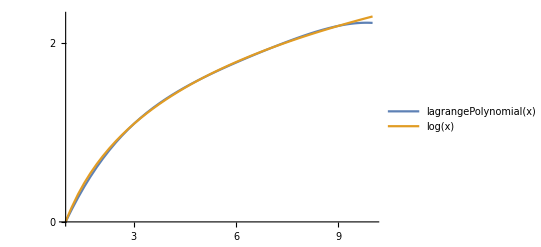

```mathematica
Plot[{lagrangePolynomial[x],Log[x]},{x,1,10},
Ticks->{Range[0,10]},PlotLegends->"Expressions"]
```

```mathematica
nodes={-1,0,1,2};
values={5,1,1,11};
lagrangePolynomial[x_]=LagrangePolynomial[nodes,values]
```

List of points and function values are not of samesize

-5/6 (1-x) (2-x) x+1/2 (1-x) (2-x) (1+x)+1/2 (2-x) x (1+x)+11/6 (-1+x) x (1+x)

```mathematica
Simplify[
-5/6 (1-x) (2-x) x+1/2 (1-x) (2-x) (1+x)+1/2 (2-x) x (1+x)+11/6 (-1+x) x (1+x)]
```

1-3 x+2 x^2+x^3

```mathematica
lagrangePolynomial[1.5]
```

4.375